## MICA: Measurement, Instrumentation, Control & Analysis

## Thermocouples

#### Ariel Mobius, 9 March 2026

#### Revisions

2025		Feb 	22	Started
2026		Mar	02	Added some material

#### Objectives

To discuss temperature measurement using thermocouples. The problem of predicting temperature from measurements of the mV level voltages coming from thermocouples is discussed. The famous thermocouple data from NIST (US National Institute of Science and Technology) are down loaded and used to illustrate how to fit various models relating temperature to thermocouple voltage as well as the reverse challenge of doing the reverse, namely to predicted temperature from measurements of thermocouple voltage. In the process we discuss both model fitting, function interpolation and inverse function (reversion) determination.

#### Keywords

Thermocouple, Thermocouple Bead, Seebeck Effect,  Type K Thermocouple, Type J Thermocouple, Curve Fitting, Least Squares Objective Functions, Average Squared Error vs Maximum Absolute Error (MinMax), Interpolating Functions, Inverse Functions, Reversion, Numerical Error, Residuals, Estimation Error, Polynomial, n-th Order Polynomial, Spline Interpolation, Hermite Polynomial Interpolation

#### Notes

Code that must be evaluated for the subsequent code to run properly starts with a black square (■). You click on this square to evaluate the adjacent code. All other code may be optionally evaluated in the usual way (Shift Enter or on a numerical key pad: Enter).

#### Thermocouples

It was noticed by the German physicist Thomas Seebeck in 1821  that when two dissimilar metals are welded or clamped together that a small voltage is generated which increases nonlinearly with temperature. This is the principle by which thermocouples work (see https://en.wikipedia.org/wiki/Thermocouple ).

Thermocouples are one of the most commonly used thermal sensors. There are many different types of thermocouples. Some are much more sensitive (mV/°C) than others, and so are suitable for very low temperatures and others for very high temperatures. Type K (consisting of the alloys chromel and alumel) and Type J (consisting of iron and the alloy constantan) are the most commonly used types.

Without calibration it is difficult to get temperature measurements to much better than ±1 °C. 

The typical measurement configuration is shown in the figure below (which is taken from https://en.wikipedia.org/wiki/Thermocouple ):

-Graphics-

There are actually 4 voltages generated in the circuit above:
1. the temperature difference between T_sense and T_ref in the chromel wire gives rise to V_1
2. the temperature difference between T_sense and T_ref in the alumel wire gives rise to V_2
3. the temperature difference between T_ref and T_meter in the upper copper wire gives rise to V_3
4.  the temperature difference between T_ref and T_meter in the lower copper wire gives rise to V_4

V_3 =  V_4 and so they cancel out. It also means that the value of T_meter does not matter. The value of T_ref does matter and in a typical thermocouple circuit it is measured using a separate temperature sensor (typically a calibrated semiconductor temperature sensor). In the case of the NIST data analyzed below T_ref is an ice bath and so = 0 °C. 
Only V_1 and V_2 contribute to the overall voltage, V.  For this reason it is common to think of the temperature measurement as only “coming” from the thermocouple bead temperature, T_sense and not the rest of the thermocouple wire.

#### Thermocouple Data

NIST makes available raw thermocouple data. The measurement of thermocouple voltage was made by NIST using the circuit shown above with the 2 reference junctions sitting in an ice bath at 0 °C (i.e.,  T_ref = 0 °C) .

The output voltage of this configuration is 0 V at 0 °C (see plot below). NIST measured the voltage generated every 1 °C increment over a range of temperatures they deemed reasonable for a range of different thermocouple types  (B, E, J, K, N, R, S, and T).
NIST also provides the coefficients of high-order polynomials fitted to the data (both for T ⟶ mV and for mV  ⟶ T). Unfortunately such high-order polynomials lead to numerical errors both because of the high powers involved and often the very small values of the coefficients.

In the following we fit such higher-order polynomials, point out potential numerical problems and then show an alternative approach using interpolating functions  to get T ⟶ mV  and their inverses to get mV  ⟶ T .

#### Import NIST Thermocouple Data

The data can be imported from NIST or from the following source in .csv file format. Here we Import[] in to the Mathematica Tabular data type which allows us to scroll through data sets in a spread-sheet like manner:

http://www.mosaic-industries.com/embedded-systems/microcontroller-projects/temperature-measurement/thermocouple/type-k-calibration-table

```mathematica
"■";  file="C:\Users\ariel\Downloads\NIST Thermocouple Data.csv";
data=Import[file,"Tabular"]
```

#### Extract Individual Thermocouple Type Data Sets

Note that the data start at row 6. The first thing we need to do is to convert from the Tabular column to a list using Normal[]. If you scroll down the Tabular data set shown above you will see blank cells. We need to exclude these and use DeleteMissing[] for this. We also have to convert the cells from strings to numbers and use ToExpression[] for this:

```mathematica
"■";  
typeBtemp=ToExpression[DeleteMissing[Normal[data[[6;;All,1]]]]];
typeBmV=ToExpression[DeleteMissing[Normal[data[[6;;All,2]]]]];

typeEtemp=ToExpression[DeleteMissing[Normal[data[[6;;All,3]]]]];
typeEmV=ToExpression[DeleteMissing[Normal[data[[6;;All,4]]]]];

typeJtemp=ToExpression[DeleteMissing[Normal[data[[6;;All,5]]]]];
typeJmV=ToExpression[DeleteMissing[Normal[data[[6;;All,6]]]]];

typeKtemp=ToExpression[DeleteMissing[Normal[data[[6;;All,7]]]]];
typeKmV=ToExpression[DeleteMissing[Normal[data[[6;;All,8]]]]];

typeNtemp=ToExpression[DeleteMissing[Normal[data[[6;;All,9]]]]];
typeNmV=ToExpression[DeleteMissing[Normal[data[[6;;All,10]]]]];

typeRtemp=ToExpression[DeleteMissing[Normal[data[[6;;All,11]]]]];
typeRmV=ToExpression[DeleteMissing[Normal[data[[6;;All,12]]]]];

typeStemp=ToExpression[DeleteMissing[Normal[data[[6;;All,13]]]]];
typeSmV=ToExpression[DeleteMissing[Normal[data[[6;;All,14]]]]];

typeTtemp=ToExpression[DeleteMissing[Normal[data[[6;;All,15]]]]];
typeTmV=ToExpression[DeleteMissing[Normal[data[[6;;All,16]]]]];
```

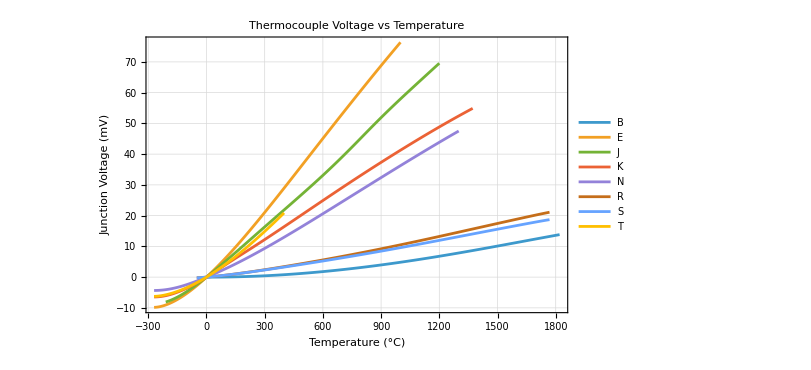

```mathematica
"■";  ListLinePlot[{{typeBtemp,typeBmV}ᵀ,{typeEtemp,typeEmV}ᵀ,{typeJtemp,typeJmV}ᵀ,{typeKtemp,typeKmV}ᵀ,
{typeNtemp,typeNmV}ᵀ,{typeRtemp,typeRmV}ᵀ,{typeStemp,typeSmV}ᵀ,{typeTtemp,typeTmV}ᵀ},
PlotRange->All,PlotTheme->"Detailed",FrameLabel->{"Temperature (°C)","Junction Voltage (mV)"},LabelStyle->{12,Black},PlotLabel->"Thermocouple Voltage vs Temperature",PlotLegends->{"B","E","J","K","N","R","S","T"},ImageSize->600]
```

#### Fit 1st-Order Polynomial to Type K Thermocouple Data

```mathematica
"■";  (* Fit a straight line *)
fittedPolynomial1=Fit[{typeKtemp,typeKmV}ᵀ,{1,t},t];
```

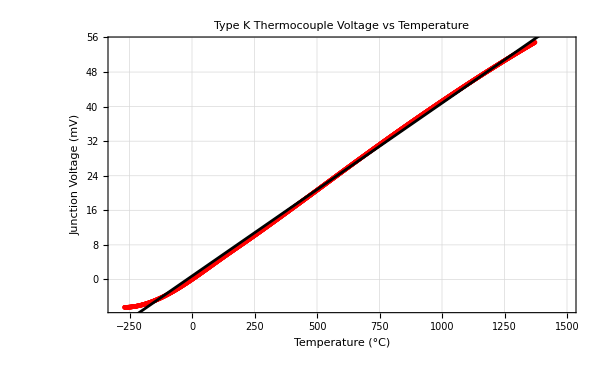

```mathematica
"■";  Show[
ListPlot[{typeKtemp,typeKmV}ᵀ,PlotRange->{{-300,1500},All},PlotStyle->Red,PlotTheme->"Detailed",FrameLabel->{"Temperature (°C)","Junction Voltage (mV)"},LabelStyle->{12,Black},PlotLabel->"Type K Thermocouple Voltage vs Temperature",ImageSize->600],
Plot[fittedPolynomial1,{t,-300,1400},PlotStyle->Black]
]
```

```mathematica
"■";  (* Calculate the residuals *)
residuals1=typeKmV-(fittedPolynomial1 /. t->typeKtemp);
```

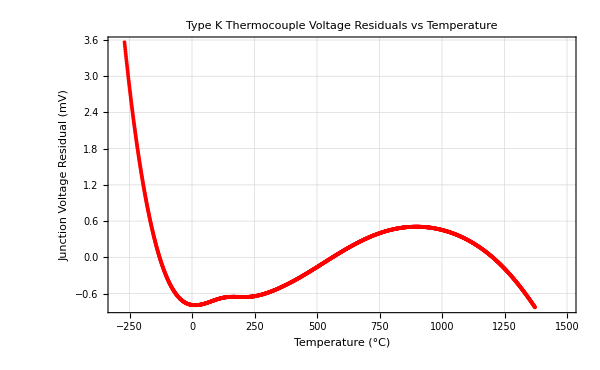

```mathematica
"■";  ListPlot[{typeKtemp,residuals1}ᵀ,PlotRange->{{-300,1500},All},PlotStyle->Red,PlotTheme->"Detailed",FrameLabel->{"Temperature (°C)","Junction Voltage Residual (mV)"},LabelStyle->{12,Black},PlotLabel->"Type K Thermocouple Voltage Residuals vs Temperature",ImageSize->600]
```

```mathematica
"■";  maxResidual1=Max[Abs[residuals1]]
```

3.56182

This is unacceptably high maximum error.
Lets try a second-order polynomial fit:

#### Fit 2nd-Order Polynomial to Type K Thermocouple Data

```mathematica
"■";  (* Fit a quadratic polynomial *)
fittedPolynomial2=Fit[{typeKtemp,typeKmV}ᵀ,{1,t,t^2},t];
```

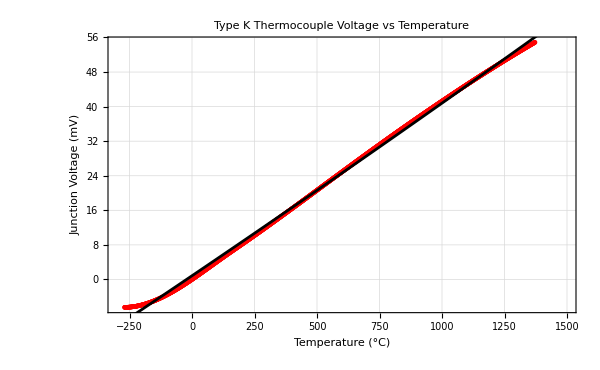

```mathematica
"■";  Show[
ListPlot[{typeKtemp,typeKmV}ᵀ,PlotRange->{{-300,1500},All},PlotStyle->Red,PlotTheme->"Detailed",FrameLabel->{"Temperature (°C)","Junction Voltage (mV)"},LabelStyle->{12,Black},PlotLabel->"Type K Thermocouple Voltage vs Temperature",ImageSize->600],
Plot[fittedPolynomial2,{t,-300,1400},PlotStyle->Black]
]
```

```mathematica
"■";  (* Calculate the residuals *)
residuals2=typeKmV-(fittedPolynomial2 /. t->typeKtemp);
```

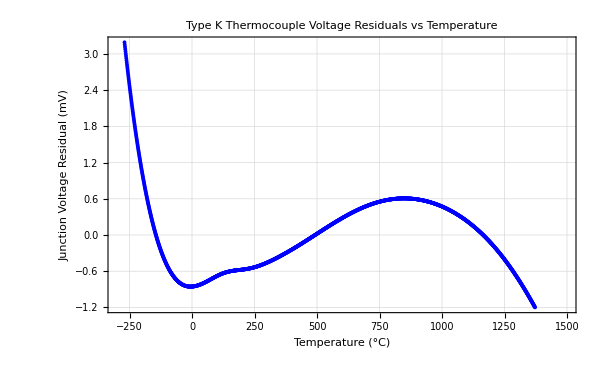

```mathematica
"■";  ListPlot[{typeKtemp,residuals2}ᵀ,PlotRange->{{-300,1500},All},PlotStyle->Blue,PlotTheme->"Detailed",FrameLabel->{"Temperature (°C)","Junction Voltage Residual (mV)"},LabelStyle->{12,Black},PlotLabel->"Type K Thermocouple Voltage Residuals vs Temperature",ImageSize->600]
```

```mathematica
"■";  maxResidual2=Max[Abs[residuals2]]
```

3.19254

This is still an unacceptably high maximum error.

#### Fit 6th-Order Polynomial to Type K Thermocouple Data

Lets fit an even higher order polynomial:

```mathematica
"■";  (* Fit a 6th order polynomial *)
fittedPolynomial6=Fit[{typeKtemp,typeKmV}ᵀ,{1,t,t^2,t^3,t^4,t^5,t^6},t];
```

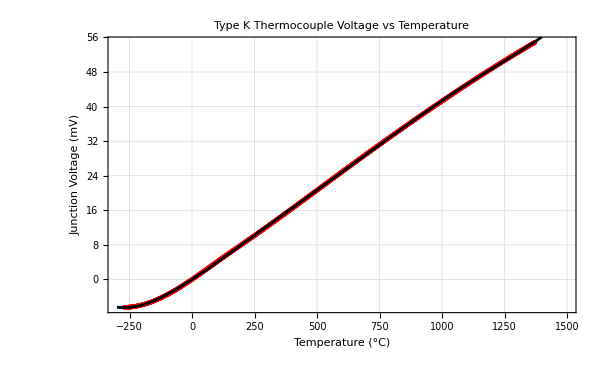

```mathematica
"■";  Show[
ListPlot[{typeKtemp,typeKmV}ᵀ,PlotRange->{{-300,1500},All},PlotStyle->Red,PlotTheme->"Detailed",FrameLabel->{"Temperature (°C)","Junction Voltage (mV)"},LabelStyle->{12,Black},PlotLabel->"Type K Thermocouple Voltage vs Temperature",ImageSize->600],
Plot[fittedPolynomial6,{t,-300,1400},PlotStyle->Black]
]
```

The fit now looks much better.

```mathematica
"■";  (* Calculate the residuals *)
residuals6=typeKmV-(fittedPolynomial6 /. t->typeKtemp);
```

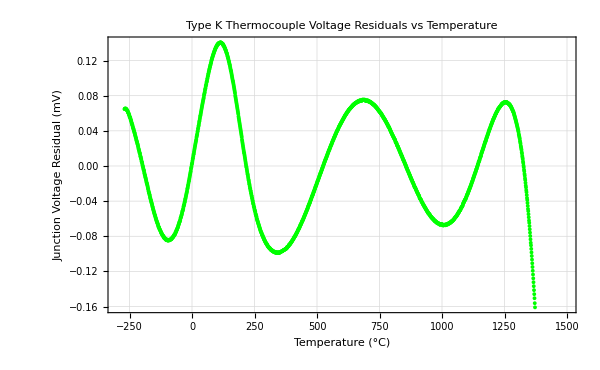

```mathematica
"■";  ListPlot[{typeKtemp,residuals6}ᵀ,PlotRange->{{-300,1500},All},PlotStyle->Green,PlotTheme->"Detailed",FrameLabel->{"Temperature (°C)","Junction Voltage Residual (mV)"},LabelStyle->{12,Black},PlotLabel->"Type K Thermocouple Voltage Residuals vs Temperature",ImageSize->600]
```

```mathematica
"■";  maxResidual6=Max[Abs[residuals6]]
```

0.160861

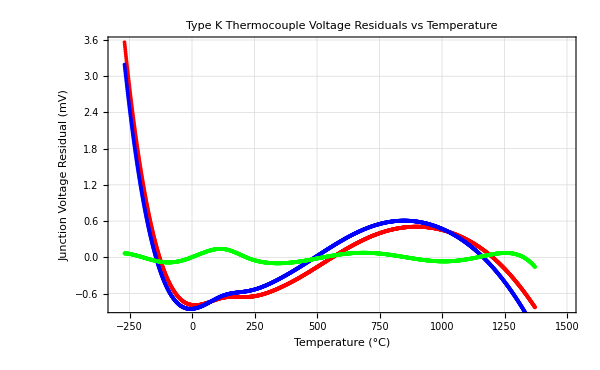

```mathematica
"■";  Show[
ListPlot[{typeKtemp,residuals1}ᵀ,PlotRange->{{-300,1500},All},PlotStyle->Red,PlotTheme->"Detailed",FrameLabel->{"Temperature (°C)","Junction Voltage Residual (mV)"},LabelStyle->{12,Black},PlotLabel->"Type K Thermocouple Voltage Residuals vs Temperature",ImageSize->600],
ListPlot[{typeKtemp,residuals2}ᵀ,PlotRange->{{-300,1500},All},PlotStyle->Blue],
ListPlot[{typeKtemp,residuals6}ᵀ,PlotRange->{{-300,1500},All},PlotStyle->Green]
]
```

#### Fit 10th-Order Polynomial to Type K Thermocouple Data

Lets fit an even higher order polynomial:

```mathematica
"■";  (* Fit a 10th order polynomial *)
fittedPolynomial10=Fit[{typeKtemp,typeKmV}ᵀ,{1,t,t^2,t^3,t^4,t^5,t^6,t^7,t^8,t^9,t^10},t];
```

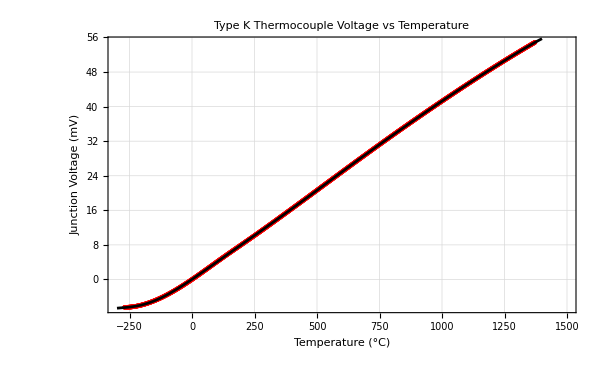

```mathematica
"■";  Show[
ListPlot[{typeKtemp,typeKmV}ᵀ,PlotRange->{{-300,1500},All},PlotStyle->Red,PlotTheme->"Detailed",FrameLabel->{"Temperature (°C)","Junction Voltage (mV)"},LabelStyle->{12,Black},PlotLabel->"Type K Thermocouple Voltage vs Temperature",ImageSize->600],
Plot[fittedPolynomial10,{t,-300,1400},PlotStyle->Black]
]
```

The fit now looks great but perhaps not significantly better than the 6th order fit?

```mathematica
"■";  (* Calculate the residuals *)
residuals10=typeKmV-(fittedPolynomial10/. t->typeKtemp);
```

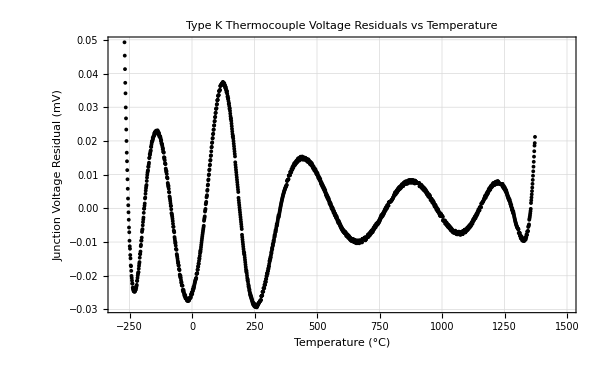

```mathematica
"■";  ListPlot[{typeKtemp,residuals10}ᵀ,PlotRange->{{-300,1500},All},PlotStyle->Black,PlotTheme->"Detailed",FrameLabel->{"Temperature (°C)","Junction Voltage Residual (mV)"},LabelStyle->{12,Black},PlotLabel->"Type K Thermocouple Voltage Residuals vs Temperature",ImageSize->600]
```

```mathematica
"■";  maxResidual10=Max[Abs[residuals10]]
```

0.0492588

```mathematica
"■";  {maxResidual1,maxResidual2,maxResidual6,maxResidual10}
```

{3.56182,3.19254,0.160861,0.0492588}

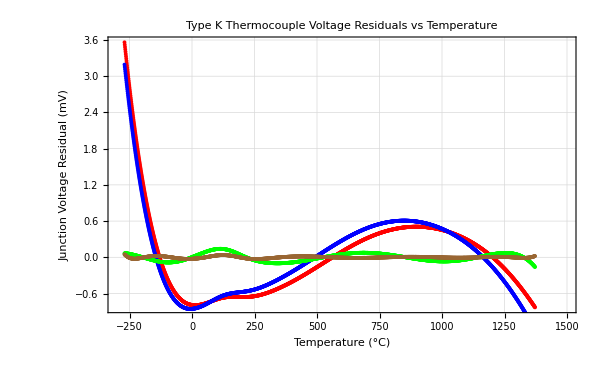

```mathematica
"■";  Show[
ListPlot[{typeKtemp,residuals1}ᵀ,PlotRange->{{-300,1500},All},PlotStyle->Red,PlotTheme->"Detailed",FrameLabel->{"Temperature (°C)","Junction Voltage Residual (mV)"},LabelStyle->{12,Black},PlotLabel->"Type K Thermocouple Voltage Residuals vs Temperature",ImageSize->600],
ListPlot[{typeKtemp,residuals2}ᵀ,PlotRange->{{-300,1500},All},PlotStyle->Blue],
ListPlot[{typeKtemp,residuals6}ᵀ,PlotRange->{{-300,1500},All},PlotStyle->Green],
ListPlot[{typeKtemp,residuals10}ᵀ,PlotRange->{{-300,1500},All},PlotStyle->Brown]
]
```

Lets look at the best fit 10-order polynomial :

```mathematica
"■";  fittedPolynomial10
```

0.0251408+0.039242 t+0.0000204082 t^2-1.11222×10^-7 t^3+2.28614×10^-10 t^4+9.77651×10^-14 t^5-1.12995×10^-15 t^6+1.92844×10^-18 t^7-1.56211×10^-21 t^8+6.33725×10^-25 t^9-1.03661×10^-28 t^10

Notice that we have very small numbers multiplying the temperature, t, raise to very high powers. This can lead to numerical problems particularly of the processor undertaking the calculation, such as a microcontroller, is using single precision floating point numbers.
A better strategy is to fit rational polynomials. If the objective is to minimize that maximum error (as opposed to the average error squared) then rational Chebyshev polynomials should be considered. Minimizing the maximum error called MinMax parameter estimation.

#### Interpolating Polynomials

Instead of fitting a single high order polynomial we can fit what are called piece-wise interpolation functions. Such functions pass through all the data points and so the residuals should be 0:

```mathematica
"■";  interpolatingFn=Interpolation[{typeKtemp,typeKmV}ᵀ]
```

InterpolatingFunction[…]

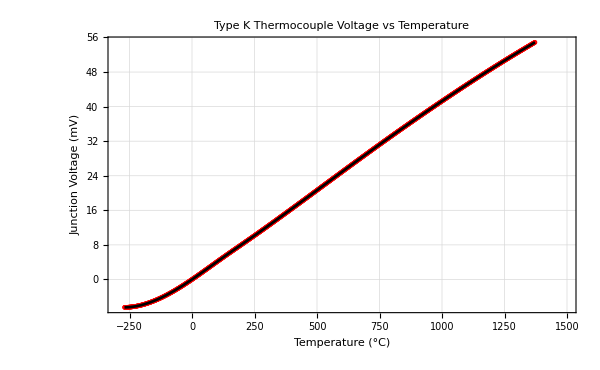

```mathematica
"■";  Show[
ListPlot[{typeKtemp,typeKmV}ᵀ,PlotRange->{{-300,1500},All},PlotStyle->Red,PlotTheme->"Detailed",FrameLabel->{"Temperature (°C)","Junction Voltage (mV)"},LabelStyle->{12,Black},PlotLabel->"Type K Thermocouple Voltage vs Temperature",ImageSize->600],
Plot[interpolatingFn[t],{t,typeKtemp[[1]],typeKtemp[[-1]]},PlotStyle->Black]
]
```

Notice that we used typeKtemp[[-1]] to return the last element of the typeKtemp list. If we try to evaluate the fittedInterpolatingPolynomial beyond the original list of temperatures we get an warning the first time it is evaluated at that value and it returns a meaningless result.

```mathematica
"■";  interpolatingFn[1500]
```

InterpolatingFunction::dmval: Input value {1500} lies outside the range of data in the interpolating function. Extrapolation will be used.

783.014

```mathematica
"■";  (* Calculate the residuals *)
residuals=typeKmV-(interpolatingFn[t]/. t->typeKtemp);
```

```mathematica
"■";  Max[Abs[residuals]]
```

0.

This shows that we our interpolating function passes through all the data points. Values in between the original data points are determined via linear interpolation between the 2 immediately adjacent data points unless a higher order interpolation function is requested (e.g., splines or Hermite polynomials).

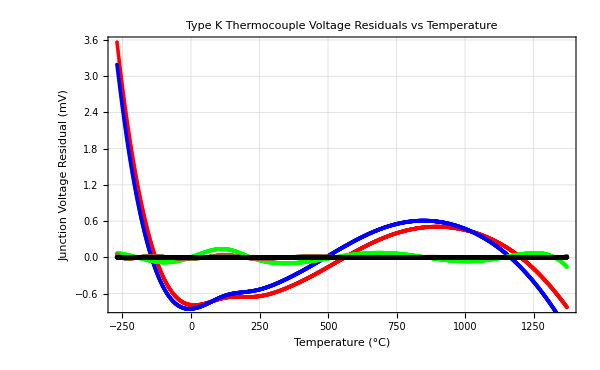

```mathematica
"■";  Show[
ListPlot[{typeKtemp,residuals1}ᵀ,PlotRange->{{typeKtemp[[1]],typeKtemp[[-1]]},All},PlotStyle->Red,PlotTheme->"Detailed",FrameLabel->{"Temperature (°C)","Junction Voltage Residual (mV)"},LabelStyle->{12,Black},PlotLabel->"Type K Thermocouple Voltage Residuals vs Temperature",ImageSize->600],
ListPlot[{typeKtemp,residuals2}ᵀ,PlotRange->{{typeKtemp[[1]],typeKtemp[[-1]]},All},PlotStyle->Blue],
ListPlot[{typeKtemp,residuals6}ᵀ,PlotRange->{{typeKtemp[[1]],typeKtemp[[-1]]},All},PlotStyle->Green],
ListPlot[{typeKtemp,residuals10}ᵀ,PlotRange->{{typeKtemp[[1]],typeKtemp[[-1]]},All},PlotStyle->Brown],
ListPlot[{typeKtemp,residuals}ᵀ,PlotRange->{{typeKtemp[[1]],typeKtemp[[-1]]},All},PlotStyle->Black]
]
```

#### Determine the Inverse Function (Reversion)

Once we have the interpolating function relating temperature to thermocouple voltage we can ask is there a way to do the reverse: namely to find a function that predicts temperature from thermocouple voltage. 
Yes, we can using InverseFunction[].

For example if we specify:

```mathematica
"■";  InverseFunction[Sin]
```

ArcSin

we get the expected ArcSin.

Lets try it for our interpolatingFun:

```mathematica
"■";  interpolatingFnInv=InverseFunction[interpolatingFn]
```

InverseFunction[InterpolatingFunction[…]]

We can check against the original data (but now we plot thermocouple temperature as a function of thermocouple voltage):

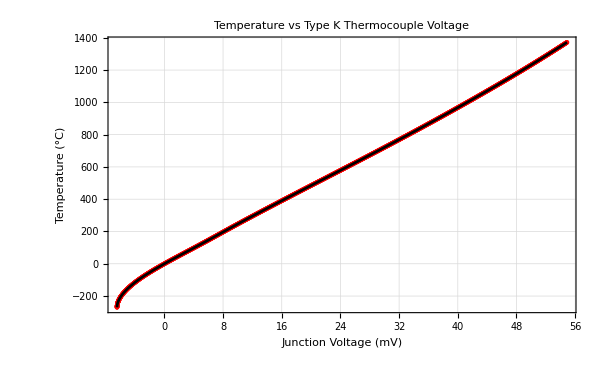

```mathematica
"■";  Show[
ListPlot[{typeKmV,typeKtemp}ᵀ,PlotRange->All,PlotStyle->Red,PlotTheme->"Detailed",FrameLabel->{"Junction Voltage (mV)","Temperature (°C)"},LabelStyle->{12,Black},PlotLabel->"Temperature vs Type K Thermocouple Voltage",ImageSize->600],
Plot[interpolatingFnInv[v],{v,typeKmV[[1]],typeKmV[[-1]]},PlotStyle->Black]
]
```

This exactly the function we need in practice where we have measured the thermocouple voltage and now want to predict the temperature that generated it.

For example if we were to boil some water and record the temperature with a type K thermocouple and measure 4.1 mV then the corresponding temperature would be (in °C):

```mathematica
interpolatingFnInv[4.1]
```

100.096